```mathematica
w[k_,h_]:=Sqrt[g*k*Tanh[k*h]];
CForm[w[k,h]]
```

3.132091952673165*Sqrt(k*Tanh(80*k))

```mathematica
Simplify@D[w[k,h],k]
CForm[%]
```

(1.56605 (80 k Sech[80 k]^2+Tanh[80 k]))/(√(k Tanh[80 k]))

(1.5660459763365826*(80*k*Power(Sech(80*k),2) + Tanh(80*k)))/Sqrt(k*Tanh(80*k))

{6.,{{L→-56.2072},{L→56.2072}}}
{6.5,{{L→-65.9653},{L→65.9653}}}
{7.,{{L→-76.5039},{L→76.5039}}}
{7.5,{{L→-87.8218},{L→87.8218}}}
{8.,{{L→-99.9153},{L→99.9153}}}
{8.5,{{L→-112.774},{L→112.774}}}
{9.,{{L→-126.377},{L→126.377}}}

{{6.,56.2072},{6.5,65.9653},{7.,76.5039},{7.5,87.8218},{8.,99.9153},{8.5,112.774},{9.,126.377}}

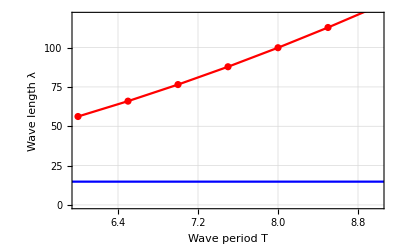

{6.,{{L→-56.2072},{L→56.2072}}}
{6.5,{{L→-65.9653},{L→65.9653}}}
{7.,{{L→-76.5039},{L→76.5039}}}
{7.5,{{L→-87.8218},{L→87.8218}}}
{8.,{{L→-99.9153},{L→99.9153}}}
{8.5,{{L→-112.774},{L→112.774}}}
{9.,{{L→-126.377},{L→126.377}}}

```mathematica
h=80;
g=9.81;
Column[tab=Table[{T,NSolve[Sqrt[g*(2π)/L*Tanh[(2π)/L*h]]==(2π)/T,L,Reals]},{T,6,9,0.5}],Frame->All]
tab=Table[{tab[[i]][[1]],L/.tab[[i]][[2]][[2]]},{i,1,Length[tab],1}]
Show[
ListPlot[tab,FrameLabel->{"Wave period T","Wave length λ"},Frame->True,GridLines->Automatic,FrameStyle->Black,PlotStyle->Red,Joined->True,Mesh->All],
ListPlot[{{5,14.8},{10,14.8}},Joined->True,PlotStyle->Blue],
PlotRange->{{6,9},{0,120}}
]
```

```mathematica
ClearAll["Global`*"]
Dj[kj_,h_]:=(kj*h)/2((kj*h)/(Sinh[kj*h]*Cosh[kj*h])+1);
c0[w_,kj_,h_,l_,d_]:=1/Dj[kj,h]((w*w*h)/g-h/(h+l)+h/(h+l)*Cosh[kj*d]/Cosh[kj*h])
FullSimplify@c0[w,k,h,l,d]
CForm[%]
```

(2 (-g+(h+l) w^2+g Cosh[d k] Sech[h k]))/(g k (h+l) (1+2 h k Csch[2 h k]))

(2*(-g + (h + l)*Power(w,2) + g*Cosh(d*k)*Sech(h*k)))/
   (g*k*(h + l)*(1 + 2*h*k*Csch(2*h*k)))

```mathematica
ArcTan[(A/c0*Sin[w*t])/(h+l)]
```

ArcTan[(A Sin[t w])/(c0 (h+l))]

```mathematica
theta[t_]:=ArcTan[(A*Sin[w*t])/((h+l)*c0[w,k,h,l,d])]
FullSimplify@theta[t]
CForm[%]
```

ArcTan[(A g k (1+2 h k Csch[2 h k]) Sin[t w])/(2 (-g+(h+l) w^2+g Cosh[d k] Sech[h k]))]

ArcTan((A*g*k*(1 + 2*h*k*Csch(2*h*k))*Sin(t*w))/
    (2.*(-g + (h + l)*Power(w,2) + g*Cosh(d*k)*Sech(h*k))))